# Free precession case

## Numerical solutions

```mathematica
free1[I1_,I2_,I3_,θ_,P_]:=Module[{sol},
ϵ=(I3-I1)/I1;
ϵ1=(I2-I1)/I1;
ω0=2π/P;
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t],u2'[t]==(ϵ*ω0*u1[t]*u3[t])/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t])/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,5*10^7},Method->"ExplicitRungeKutta"]
; sol]
```

### A case with m<1

0.704088

{{u1→InterpolatingFunction[…],u2→InterpolatingFunction[…],u3→InterpolatingFunction[…]}}

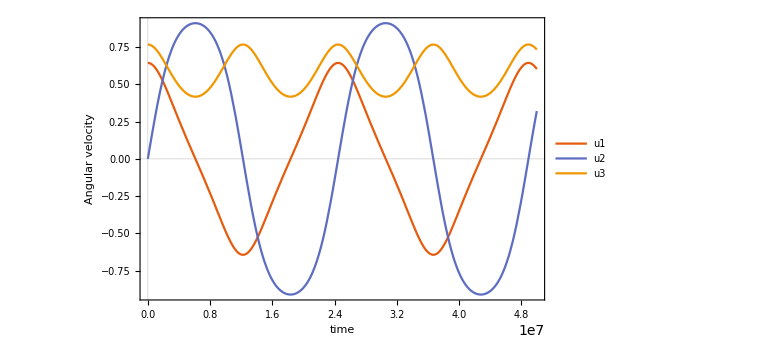

```mathematica
I1=1;I2=1.0+5*10^-8;I3=1+10^-7;θ0=40/180*π;P=1;
δ=(I3(I2-I1))/(I1(I3-I2));
m=δ*Tan[θ0]^2;
Print[m];
sol=Evaluate[free1[I1,I2,I3,θ0,P]]
Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,5*10^7},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]
```

### A case with m>1

7.54863

{{u1→InterpolatingFunction[…],u2→InterpolatingFunction[…],u3→InterpolatingFunction[…]}}

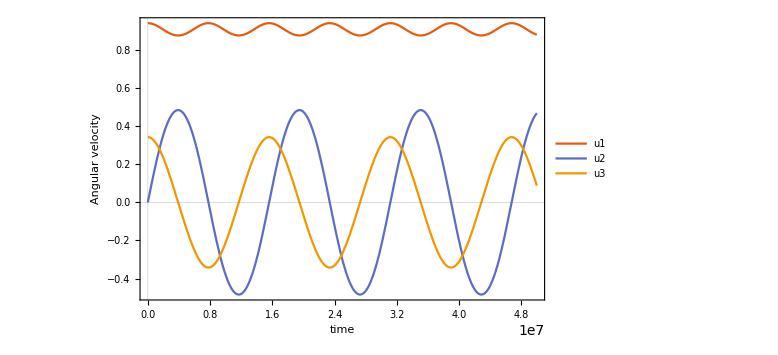

```mathematica
I1=1;I2=1.0+5*10^-8;I3=1+10^-7;θ0=70/180*π;P=1;
δ=(I3(I2-I1))/(I1(I3-I2));
m=δ*Tan[θ0]^2;
Print[m];
sol=Evaluate[free1[I1,I2,I3,θ0,P]]
Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,5*10^7},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]
```

0.

{{u1→InterpolatingFunction[…],u2→InterpolatingFunction[…],u3→InterpolatingFunction[…]}}

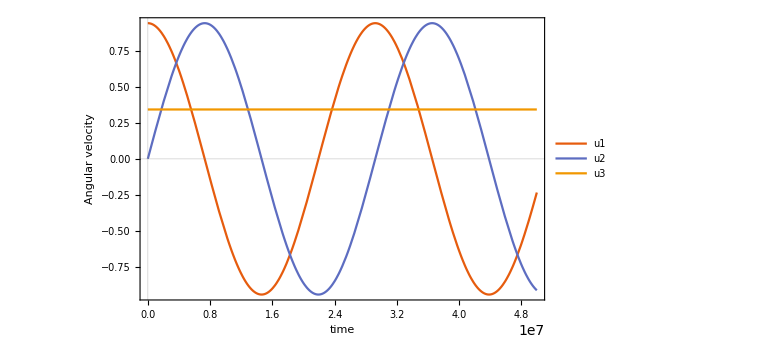

```mathematica
I1=1;I2=1.0;I3=1+10^-7;θ0=70/180*π;P=1;
δ=(I3(I2-I1))/(I1(I3-I2));
m=δ*Tan[θ0]^2;
Print[m];
sol=Evaluate[free1[I1,I2,I3,θ0,P]]
Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,5*10^7},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]
```

## m<1 case: Analytical solution

```mathematica
free2[I1_,I2_,I3_,θ0_,P_,t_]:=Module[{L1,L2,L3},
ϵ=(I3-I1)/I1;
δ=(I3(I2-I1))/(I1(I3-I2));
ω0=2π/P;
m=δ*Tan[θ0]^2;
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
L1=Sin[θ0]*JacobiCN[ωp*t,m];
L2=Sin[θ0]*(1+δ)^0.5*JacobiSN[ωp*t,m];
L3=Cos[θ0]*JacobiDN[ωp*t,m];
{L1,L2,L3}

]
```

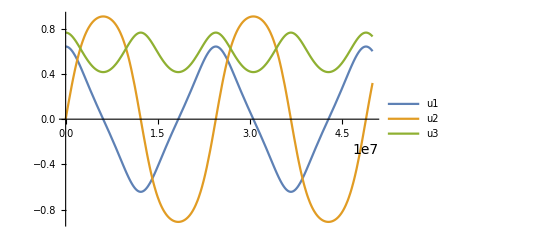

```mathematica
I1=1;I2=1.0+5*10^-8;I3=1+10^-7;θ0=40/180*π;P=1;

Plot[{free2[I1,I2,I3,θ0,P,t][[1]],free2[I1,I2,I3,θ0,P,t][[2]],free2[I1,I2,I3,θ0,P,t][[3]]},{t,0,5*10^7},Background->White,PlotLegends->{"u1","u2","u3"}]
```

## m>1 case

```mathematica
free3[I1_,I2_,I3_,θ0_,P_,t_]:=Module[{L1,L2,L3},
I11=I3;
I33=I1;
I22=I2;
ϵ=(I33-I11)/I11;
δ=(I33(I22-I11))/(I11(I33-I22));
θ1=π/2-θ0;
ω0=2π/P;
m=δ*Tan[θ1]^2;
L=(I11^2*ω0^2*Sin[θ1]^2+I33^2*ω0^2*Cos[θ1]^2)^0.5;
ωp=ϵ*L*Cos[θ1]/(I33(1+δ)^0.5);
m=δ*Tan[θ1]^2;
L1=Sin[θ1]*JacobiCN[ωp*t,m];
L2=Sin[θ1]*(1+δ)^0.5*JacobiSN[ωp*t,m];
L3=Cos[θ1]*JacobiDN[ωp*t,m];
{L1,L2,L3}

]
```

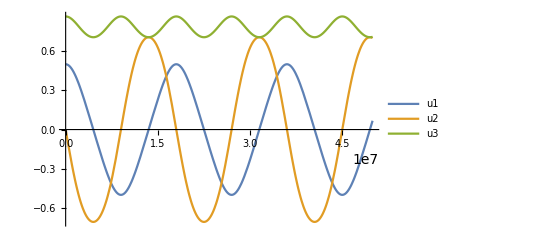

```mathematica
I1=1;I2=1.0+5*10^-8;I3=1+10^-7;θ0=60/180*π;P=1;

Plot[{free3[I1,I2,I3,θ0,P,t][[1]],free3[I1,I2,I3,θ0,P,t][[2]],free3[I1,I2,I3,θ0,P,t][[3]]},{t,0,5*10^7},Background->White,PlotLegends->{"u1","u2","u3"}]
```